# Algoritmo de Búsqueda Voraz - Estructura de Árbol

Ingreso del Grafo e iniciación de variables

```mathematica
vertex={
{0,5000,1},{2500,5000,2},{4000,5000,3},{5000,5000,4},{0,3000,5},{2000,3000,6},{2500,3000,7},{4000,2750,8},{5000,2750,9},{2000,2000,10},{2500,2000,11},{3750,2000,12},{4000,2000,13},{5000,2000,14},{3750,1250,15},{5000,1250,16},{0,500,17},{2000,500,18},{0,0,19},{2000,0,20},{3750,0,21},{5000,0,22}
};
edges={
{1,2,2500},{2,3,1500},{3,4,1000},{5,6,2000},{6,7,500},{8,9,1000},{10,11,500},{11,12,1250},{12,13,250},{13,14,1000},{15,16,1250},{17,18,2000},{19,20,2000},{20,21,1750},{21,22,1250},{4,9,2250},{9,14,750},{14,16,750},{16,22,1250},{3,8,2250},{8,13,750},{12,15,750},{15,21,1250},{2,7,2000},{7,11,1000},{6,10,1000},{10,18,1500},{18,20,500},{1,5,2000},{5,17,2500},{17,19,500}
};
```

Obtención de los Polígonos del Grafo

```mathematica
GetPolygons[v0_,c0_]:=Module[{v,polygons,vertexX,vertexY,vertexXY,vertexYX,n0,m0,i,j,k,p},
v=Map[{c0[[#]][[1]],c0[[#]][[2]],v0[[#]]}&,Range[Length[v0]]];
polygons={};
For[i=1,i≤Length[v],i++,
vertexX={};
vertexY={};
For[j=1,j≤Length[v],j++,
If[v[[i]][[2]]==v[[j]][[2]]&&v[[i]][[1]]<v[[j]][[1]],
vertexX=Append[vertexX,v[[j]]];
,If[v[[i]][[1]]==v[[j]][[1]]&&v[[i]][[2]]>v[[j]][[2]],
vertexY=Append[vertexY,v[[j]]];
]
]
];
If[(Length[vertexX]*Length[vertexY])≠0,
vertexXY={};
vertexYX={};
n0;
m0;
vertexX=Sort[vertexX,#1[[1]]<#2[[1]]&];
vertexY=Sort[vertexY,#1[[2]]>#2[[2]]&];
For[j=1,j≤Length[vertexX],j++,
p=False;
For[k=1,k≤Length[v],k++,
If[vertexX[[j]][[1]]==v[[k]][[1]]&&vertexX[[j]][[2]]>v[[k]][[2]],
vertexXY=Append[vertexXY,v[[k]]];
p=True;
]
];
If[p,
n0=j;
vertexXY=Sort[vertexXY,#1[[2]]>#2[[2]]&];
Break[];
]
];
For[j=1,j≤Length[vertexY],j++,
p=False;
For[k=1,k≤Length[v],k++,
If[vertexY[[j]][[2]]==v[[k]][[2]]&&vertexY[[j]][[1]]<v[[k]][[1]],
vertexYX=Append[vertexYX,v[[k]]];
p=True;
]
];
If[p,
m0=j;
vertexYX=Sort[vertexYX,#1[[1]]<#2[[1]]&];
Break[];
]
];
For[j=1,j≤Length[vertexXY],j++,
For[k=1,k≤Length[vertexYX],k++,
If[vertexXY[[j]]==vertexYX[[k]],
polygons=Append[polygons,Union[{v[[i]][[3]]},Take[Map[Last,vertexX,{1}],n0],Take[Map[Last,vertexY,{1}],m0],Take[Map[Last,vertexXY,{1}],j],Take[Map[Last,vertexYX,{1}],k]]];
polygons[[Length[polygons]]]=Sort[Last[polygons],#1<#2&];
Break[];
]
]
]
]
];
Return[polygons]
]
```

Obtención de los Vértices en la Frontera del Grafo

```mathematica
GetBorder[v0_,c0_]:=Module[{v,limitX,limitY,frontier0},
v=Map[{c0[[#]][[1]],c0[[#]][[2]],v0[[#]]}&,Range[Length[v0]]];
frontier0={};
limitX=Max[Map[#[[1]]&,v]];
limitY=Max[Map[#[[2]]&,v]];
For[i=1,i≤Length[v],i++,
If[v[[i]][[1]]*v[[i]][[2]]==0||v[[i]][[1]]==limitX||v[[i]][[2]]==limitY,
frontier0=Append[frontier0,v[[i]][[3]]];
]
];
Return[frontier0];
]
```

Creación del Grafo

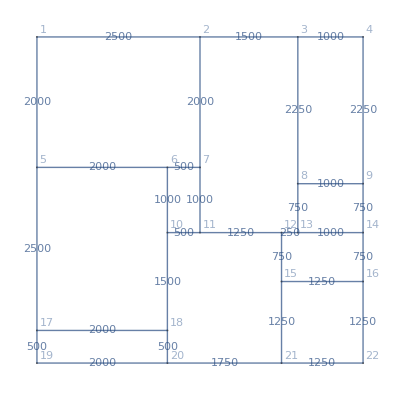

```mathematica
nEdges=Map[#_⟦1⟧<->#_⟦2⟧&,edges];
eWeigth=Map[#_⟦3⟧&,edges];
coordinates=Map[Take[#,2]&,vertex];
vertex=Map[Last,vertex,{1}];

myGraph=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
myGraphedGraph=Graph[nEdges,VertexLabels->"Name",VertexSize->Tiny,EdgeWeight->eWeigth,VertexCoordinates->coordinates,EdgeLabels->myGraph]
```

Algoritmo

```mathematica
(*Raíz, vertices, aristas, cuadriláteros, grafo*)
VoraciousSearchAlgorithm[root_,v0_,e0_,s0_,g0_]:=Module[{myRoot,v,e,s,vertexS,edgesS,squaresS,i,j,k,l,g,minimumPathDistance,minimumPath,otherMinimumPath,otherMinimumPathDistance,frontier,path,w,deletedEdges,leafVertex,vertexReduction,edgesReduction,squaresReduction,squaresReduction0,minimumDistance},

v=v0;
e=e0;
s=s0;
g=g0;
squaresS={};
vertexS={};
edgesS={};
myRoot=root;


minimumPathDistance=Infinity;
minimumPath;
otherMinimumPathDistance=Infinity;
otherMinimumPath;

deletedEdges=True;
squaresReduction=s;

(*Agregar a P(T) cada p ϵ P(G) tal que root ϵ p*)
For[i=1,i≤Length[s],i++,
For[j=1,j≤Length[s[[i]]],j++,
If[myRoot==s[[i]][[j]],
squaresS=Union[squaresS,s[[i]]];
s=Delete[s,i];
i=i-1;
Break[];
]
]
];

(*Agregar root a V'(T) y eliminarlo de V(G)*)
vertexS=Append[vertexS,myRoot];
v=Complement[v,vertexS];


(*Comienzo del Ciclo While - Búsqueda del Resto del Camino que es Solución al Problema MLC*)
While[Length[s]≠0,
frontier={};
For[i=1,i≤Length[s],i++,
frontier=Union[frontier,Intersection[s[[i]],squaresS]]
];

For[i=1,i≤Length[frontier],i++,
For[j=1,j≤Length[v],j++,
If[frontier[[i]]≠v[[j]],
path=FindShortestPath[g,frontier[[i]],v[[j]]];
w=GraphDistance[g,frontier[[i]],v[[j]],Method->"Dijkstra"];
If[w<minimumPathDistance,
minimumPathDistance=w;
minimumPath=path;

]
]
]
];
For[i=1,i≤Length[vertexS],i++,
For[j=1,j≤Length[minimumPath],j++,
path=FindShortestPath[g,vertexS[[i]],minimumPath[[j]]];
w=GraphDistance[g,vertexS[[i]],minimumPath[[j]],Method->"Dijkstra"];
If[w<otherMinimumPathDistance,
otherMinimumPathDistance=w;
otherMinimumPath=path;
]
]
];
edgesS=Join[edgesS,Map[{minimumPath[[#]],minimumPath[[#+1]]}&,Range[Length[minimumPath]-1]],Map[{otherMinimumPath[[#]],otherMinimumPath[[#+1]]}&,Range[Length[otherMinimumPath]-1]]];
vertexS=Union[vertexS,minimumPath,otherMinimumPath];
minimumPath=Union[minimumPath,otherMinimumPath];
For[i=1,i≤Length[minimumPath],i++,
For[j=1,j≤Length[s],j++,
For[k=1,k≤Length[s[[j]]],k++,
If[minimumPath[[i]]==s[[j]][[k]],
squaresS=Union[squaresS,s[[j]]];
s=Delete[s,j];
i=i-1;
Break[];
]
]
]
];
minimumPathDistance=Infinity;
otherMinimumPathDistance=Infinity;
minimumPath={};
otherMinimumPath={};
];

(*Comienzo del Algoritmo de Reducción*)
While[deletedEdges,
leafVertex=Complement[Map[If[#[[2]]==1,#[[1]],Nothing]&,Tally[Join[Map[#[[1]]&,edgesS],Map[#[[2]]&,edgesS]]]],{myRoot}];
For[i=1,i≤Length[leafVertex],i++,
For[j=1,j≤Length[edgesS],j++,
If[leafVertex[[i]]==edgesS[[j]][[1]],
leafVertex[[i]]={leafVertex[[i]],edgesS[[j]][[2]]};
Break[],
If[leafVertex[[i]]==edgesS[[j]][[2]],
leafVertex[[i]]={leafVertex[[i]],edgesS[[j]][[1]]};
Break[]
]
]
];
For[j=1,j≤Length[e],j++,
If[leafVertex[[i]]==Take[e[[j]],2]||leafVertex[[i]]==Reverse[Take[e[[j]],2]],
leafVertex[[i]]=Join[leafVertex[[i]],{Last[e[[j]]]}]
]
]
];
leafVertex=Sort[leafVertex,#1[[3]]>#2[[3]]&];
For[i=1,i≤Length[leafVertex],i++,
vertexReduction=Complement[vertexS,{leafVertex[[i]][[1]]}];
edgesReduction=Complement[edgesS,{Take[leafVertex[[i]],2]},{Reverse[Take[leafVertex[[i]],2]]}];
squaresReduction0=squaresReduction;
For[j=1,j≤Length[vertexReduction],j++,
For[k=1,k≤Length[squaresReduction0],k++,
For[l=1,l≤Length[squaresReduction0[[k]]],l++,
If[vertexReduction[[j]]==squaresReduction0[[k]][[l]],
squaresReduction0=Delete[squaresReduction0,k];
k=k-1;
Break[];
]
]
]
];
If[Length[squaresReduction0]==0,
vertexS=vertexReduction;
edgesS=edgesReduction;
deletedEdges=True;
Break[],
deletedEdges=False;
]
];
];
minimumDistance=0;
For[i=1,i≤Length[edgesS],i++,
minimumDistance+=GraphDistance[g,edgesS[[i]][[1]],edgesS[[i]][[2]]];
];
Return[{(*HighlightGraph[myGraphedGraph,Map[First[#]<->Last[#]&,edgesS]],*)myRoot,vertexS,edgesS,minimumDistance}]

]
```

Obtención de la Raíz con el Camino más Corto

0.920406

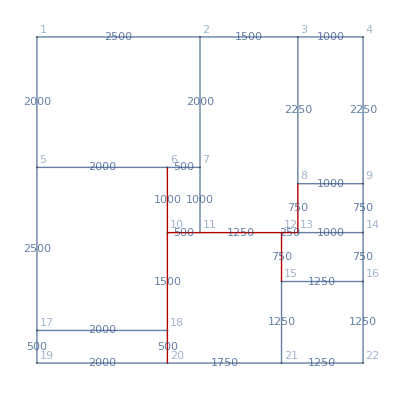

```mathematica
Time=Timing[
Results={};
squares=GetPolygons[vertex,coordinates];
border=GetBorder[vertex,coordinates];
For[i=1,i≤Length[border],i++,
Results=Append[Results,VoraciousSearchAlgorithm[border[[i]],vertex,edges,squares,myGraphedGraph]];
];
Results=Sort[Results,#1[[4]]<#2[[4]]&];
HighlightGraph[myGraphedGraph,Map[First[#]<->Last[#]&,Results[[1]][[3]]]]
];
Time[[1]]
Time[[2]]
```